```mathematica
NotebookSave[];
SetOptions[$FrontEndSession,NotebookAutoSave->True]

DD = 200; (* d, the suffix length*)

EpsRatio[eps_]:=(1+eps)/(1-eps);
H[a_]:=-a Log[2, a] - (1-a) Log[2, 1-a]; (* Binary entropy function *)
p[a_, eps_]:=p[a, eps]=(1/2)(1-eps)^(1-a)(1+eps)^a; (* The probability without the power d*)
S[d_,a_]:=S[d,a]= Sum[(Binomial[Floor[(1-a) d],t]),{t, Ceiling[a d], Ceiling[(1-a)d], 1} ]; (* Exact sum *)
ExactTermBaseVariance[a_, eps_, d_:DD]:=ExactTermBaseVariance[a, eps, d]=(S[d, a]^2Binomial[d, a d]p[a,eps]^d)^(1/d);
ExpDis1Variance[a_, eps_]:= H[a]+2(1-a)-1 +  Log[2,(1+eps)^a( 1-eps)^(1-a)]
ExpDis2Variance[a_, eps_]:= H[a]+2(1-a)H[a/(1-a)]-1 +  Log[2,(1+eps)^a( 1-eps)^(1-a)]
DaExpDis2Variance[a_, eps_]:=D[ExpDis2Variance[aa, ee],{aa,1}]/.{aa->a,ee->eps}
zOneThirdTermVariance[eps_]:=2^(H[1/3]+1/3)(1+eps)^(1/3)(1-eps)^(2/3);



(*Second Moment*)
Phi[eps_]:=(3/2)(1+eps)^(1/3)(1-eps)^(2/3)
Psi[eps_]:=(1- Log[2,(1+eps)/(1-eps)])^2 Log[2]/63
Qstar2Variance[eps_]:=Block[{a,b,c,r},
r=EpsRatio[eps];
-1/3 + Log[2,3(1+eps)^(1/3)(1-eps)^(2/3)]+ (1- Log[2,r])^2 Log[2]/63
];
Qstar2VarianceTest[eps_]:=Block[{e},
(((-21+Log[2]) Log[2]+63 Log[3-3 e]+Log[-1+2/(1+e)] (-21+Log[-4+8/(1+e)]))/(63 Log[2]))/.{e->eps}]

Manipulate[
Plot[{
Style[ExactTermBaseVariance[a, eps], Blue]

,Style[If[a≤  1/3  && eps < 1/3,2^ExpDis1Variance[a, eps] ], Green]
,Style[If[a>  1/3 && eps > 0.6,2^ExpDis2Variance[a, eps] ], Green]

,Style[If[a≤  1/3 && eps<  1/3,(5-3 eps)/2], Black]
,Style[If[a≤  1/3 && eps ≥ 1/3,zOneThirdTermVariance[eps]], Black]
,Style[If[a>  1/3 && eps ≤  0.6,zOneThirdTermVariance[eps]], Black]
(*Linear approx*)
(*,Style[If[a>  1/3 && eps>  0.6,2^(ExpDis2Variance[1/3,eps]+DaExpDis2Variance[1/3,eps](0.4-1/3))],Black]*)
(* Quadratic approx*)
,Style[If[a>1/3 && eps >0.6,2^Qstar2Variance[eps]],Black]
,Style[If[a>1/3 && eps >0.6,2^Qstar2VarianceTest[eps]],Red, Dashed]

},{a, 0, 1/2}, 
AxesLabel->Automatic, PlotLegends->"Expressions", PlotLabel->"Variance", PlotRange->Full
]
,{{eps,0},0,0.999, 0.01}] (*<------------------------------------------------------------------------------------*)
```

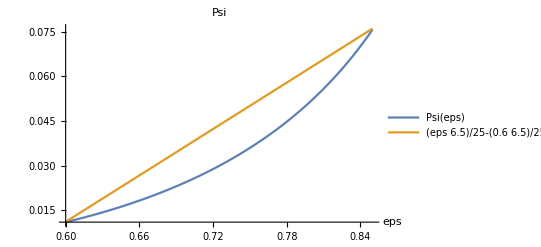

```mathematica
Manipulate[
Manipulate[
Plot[{
Style[If[a ≤  1/3 && eps<  1/3,(5-3 eps)/2], Black]
,Style[If[a ≤  1/3 && eps ≥ 1/3,zOneThirdTermVariance[eps]], Purple]
,Style[If[a > 1/3 && eps ≤  0.6,zOneThirdTermVariance[eps]], Purple]
(*Linear approx*)
(*,Style[If[a>  1/3 && eps>  0.6,2^(ExpDis2Variance[1/3,eps]+DaExpDis2Variance[1/3,eps](0.4-1/3))],Black]*)
(* Quadratic approx*)
,Style[If[a > 1/3 && eps >0.6,2^Qstar2Variance[eps]],Blue]
,Style[If[a > 1/3 && eps >  0.6,zOneThirdTermVariance[eps]], Purple, Dotted]
},{eps, 0, 1}, 
AxesLabel->Automatic, PlotLegends->"Expressions", PlotLabel->"Variance", PlotRange->Full
]
,{a,0,1/2,0.05}]
,{n,1,20,3}];

NSolve[2^{2/3+ Psi[eps]} Phi[eps]==1 && 0.6 ≤ eps ≤ 1,eps];
Plot[{Psi[eps]
,eps * 6.5/25 - 0.6*6.5/25 + 0.0111
},
 {eps, 0.6, 0.85}
,AxesLabel->Automatic, PlotLegends->"Expressions", PlotLabel->"Psi", PlotRange->Full]
```

```mathematica
Manipulate[
Manipulate[
Plot[{

Style[If[region ==1 && eps ≤ 1/3,(  ((5-3 eps)/2)^{d+1}/((5-3 eps)/2-1)  )^(1/d)], Black]
,Style[If[region ==1 && eps ≤ 1/3,(  2((5-3 eps)/2)^d  )^(1/d)], Blue]

,Style[If[region == 2 &&eps>1/3 && eps ≤ 0.6, ((2^(2/3)Phi[eps])^{d+1}/(2^(2/3)Phi[eps]-1)  )^(1/d)], Black]
,Style[If[region == 2 &&eps>1/3 && eps ≤ 0.6,(  3(2^(2/3)Phi[eps])^d  )^(1/d)], Blue]

,Style[If[region == 3 && eps > 0.6 && eps ≤ 0.80,(  2^((d+1) Qstar2Variance[eps])/(2^Qstar2Variance[eps] - 1) )^(1/d)],Black]
,Style[If[region == 3 && eps > 0.6 && eps ≤ 0.80, (  3(2^(2/3)Phi[eps])^d 2^((d+1) Psi[eps])  )^(1/d)], Blue]
(*, 3  (2^(2/3)Phi[eps])^d 2^((d+1) Psi[eps])*)
},
 {eps, 0, 1}
,AxesLabel->Automatic, PlotLegends->"Expressions", PlotLabel->"Variance"]
,{{d,40},1,40,1}]
,{region, 1, 3, 1}]
```

```mathematica
PhiHat[eps_]:=2^(2/3)Phi[eps];
VarTermLeft[eps_]:=(5-3 eps)/2;
VarTermMiddle[eps_]:= PhiHat[eps];
VarTermRight[eps_]:= PhiHat[eps]2^Psi[eps];
VarTermRightUpper[eps_]:= 2^(0.73)Phi[eps];
Manipulate[
Plot[
{
Style[If[eps < 1/3,VarTermLeft[eps]], Black],
Style[VarTermMiddle[eps], Red],
Style[If[eps>0.6,VarTermRight[eps]], Blue],
Style[If[eps>0.6,VarTermRightUpper[eps]], Purple]
},{eps, If[region==1,0,If[region==2,1/3,0.6]], If[region==1,1/3,If[region==2,0.6,0.82]]}, Epilog->{Line[{{1/3,0},{ 1/3,2.5}}], Line[{{0.6,0},{ 0.6,2.5}}]},
PlotLabel->"Variance terms"
],{region,1,3,1}]
```

```mathematica
(*Final bound, eps \in (0.6, 0.81) *)

Manipulate[
Plot[{
0,
3/4+Log[2,Phi[eps]]-2 delta
}, 
{delta, 0.7-0.48(eps + eps^2 - eps^3), 1}
(*{delta, (Log[2,3]-1/4-Log[2,E]/3 (eps + eps^2 - eps^3))/2, 1}*)
]
,{eps, 0.6, 0.81}]
```

```mathematica
Theta1[eps_]:=Log[2, (5-3 eps)/2]/2;
Theta2[eps_]:=(2/3 + Log[2, Phi[eps]])/2;
Theta3[eps_]:=(3/4 + Log[2, Phi[eps]])/2;
ThetaMean[eps_]:=Log[2, (1-eps)/2+Sqrt[1-eps^2]];

Manipulate[Manipulate[
Plot[{
Style[If[region==1 && delta >Theta1[eps], 2 (delta - Theta1[eps])], Black],
Style[If[region==2&& delta >Theta2[eps], 2 (delta - Theta2[eps])], Red],
Style[If[region==3&& delta >Theta3[eps], 2 (delta - Theta3[eps])], Blue],
Style[If[region ≤ 2 && delta >ThetaMean[eps] ,delta - ThetaMean[eps]],Green],
Style[If[region ==3 ,delta],Green]
}
(*,{delta, If[region==1,Theta1[eps], If[region==2, Theta2[eps], Theta3[eps]]], 1}*)
,{delta, 0, 1}
, PlotLabel->"Loss in delta in first- vs second-moment bounds"
,AxesLabel->Automatic
(*,Epilog->{Line[{{1/3,0},{ 1/3,1}}], Line[{{0.6,0},{ 0.6,0.81}}]}*)
],
{eps, If[region==1,0,If[region==2,1/3,0.6]], If[region==1,1/3,If[region==2,0.6,0.82]]}]
,{region,1,3,1}]
```

-0.339851